```mathematica
Quit[]
```

### In this notebook, we redefine the consistency conditions to accommodate variable step size LMMs

```mathematica
ρ[a_][xi_]:=Sum[a[[i+1]] xi^i,{i,0,Length[a]-1}]
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

#### First, we have the order conditions for a fixed step size:

```mathematica
fixedordercond[p_]:=Table[((∑_(j=0)^2 Subscript[α, j] j^(m+ϵ))==(m∑_(j=0)^2 Subscript[β, j] j^(m-1+ϵ)))/.{0^ϵ->1,ϵ->0, 0^(-1+ϵ)->0},{m,0,p}]
```

```mathematica
fixedordercond[2]
```

{α_0+α_1+α_2==0,α_1+2 α_2==β_0+β_1+β_2,α_1+4 α_2==2 (β_1+2 β_2)}

#### To change these conditions to fit variable step size methods, we go back to the truncation error, but allow h to be h_n: τ_n:=1/h_n[∑_(j=0)^k (α_(n,j)y[t_(n+j)])-h_n∑_(j=0)^k (β_(n,j)y'[t_(n+j)])]

#### ChatGPT then proposes this: Given that τ_j=t_(n+j)-t_n and h_n=t_(n+1)-t_n, let us introduce a scaling variable c_j c_j=τ_j/h_n=(t_(n+j)-t_n)/h_n This is dimensionless. Note that if we have a fixed step size, t_(n+j)=t_n+j h and so c_j=(t_(n+j)-t_n)/h=(j h)/h=j

#### We now implement the Taylor expansion: y(t_(n+j))=y(t_n+(t_(n+j)-t_n))=∑_(m=0)^∞ ((t_(n+j)-t_n)^m/(m!)y^(m)[t_n]) Recall c_j=(t_(n+j)-t_n)/h_n, therefore t_(n+j)-t_n=c_j h_n y(t_(n+j))=∑_(m=0)^∞ ((c_j h_n)^m/(m!)y^(m)[t_n])=∑_(m=0)^∞ (h_n^m c_j^m/(m!)y^(m)[t_n]) We do the same for the derivative: y'(t_(n+j))=y(t_n+(t_(n+j)-t_n))=∑_(m=0)^∞ ((c_j h_n)^m/(m!)y^(m+1)[t_n])

#### *Note that for a fixed step size, t_(n+j)=t_n+j h->t_(n+j)-t_n=j h

#### We now substitute into the LTE: LHS (α-coefficients): ∑_(j=0)^k α_(n,j)y[t_(n+j)]=∑_(m=0)^∞ (h_n^m(∑_(j=0)^k α_(n,j)c_j^m)(y^(m)[t_n])/(m!)) RHS (β-coefficients): h_n∑_(j=0)^k β_(n,j)y'[t_(n+j)]=∑_(m=0)^∞ (h_n^(m+1)(∑_(j=0)^k β_(n,j)c_j^m)(y^(m+1)[t_n])/(m!)) Shift index for RHS: =∑_(m=1)^∞ (h_n^m(∑_(j=0)^k β_(n,j)c_j^(m-1))(y^(m)[t_n])/((m-1)!))

#### Notice how similar this is to the fixed step size conditions. The only difference is we now use c_j instead of j

#### One last thing. Since we want our coefficients to be in terms of ω_i=h_i/(h_(i-1)), we will enforce that on c_j For the BDF2 method the index is shifted by 1 in Hairer, Norsett & Wanner vol 1. This changes c_j=(t_(n-1+j)-t_(n-1))/h_n j = 0: c_0=(t_(n-1)-t_(n-1))/h_n=0 j=1: c_1=(t_n-t_(n-1))/h_n=(h_(n-1))/h_n=1/ω_n j=2: c_2=(t_(n+1)-t_(n-1))/h_n=(t_(n+1)-t_n+t_n-t_(n-1))/h_n=(h_n+h_(n-1))/h_n=1+1/ω_n j=3: c_3=(t_(n+2)-t_(n-1))/h_n=(t_(n+2)-t_(n+1)+t_(n+1)-t_(n-1))/h_n=(h_(n+1)+h_n+h_(n-1))/h_n=ω_(n+1)+1+1/ω_n

#### Therefore, the consistency conditions are as follows: Order 0: ∑_(j=0)^k α_j=0 Order 1: ∑_(j=0)^k α_(n,j)c_j=∑_(j=0)^k β_(n,j) Order 2: ∑_(j=0)^k α_(n,j)c_j^2=∑_(j=0)^k β_(n,j)c_j Order 3: ∑_(j=0)^k α_(n,j)c_j^3=∑_(j=0)^k β_(n,j)c_j^2

#### We give the order conditions as a function below:

```mathematica
Clear[c]
```

```mathematica
c[j_]:=Piecewise[{{0,j==0},{1/Subscript[ω, n]+∑_(i=0)^(j-2) (∏_(l=1)^i Subscript[ω, n+l]),j>=1}}]
```

```mathematica
Table[c[i],{i,0,4}]
```

{0,1/ω_n,1+1/ω_n,1+1/ω_n+ω_(1+n),1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)}

```mathematica
variablestepcond[k_]:=Table[((∑_(j=0)^k Subscript[α, n,j] c[j]^(m+ϵ))==(m∑_(j=0)^k Subscript[β, n,j] c[j]^(m-1+ϵ)))/.{0^ϵ->1,ϵ->0, 0^(-1+ϵ)->0},{m,0,2}]
```

```mathematica
variablestepcond[2]
```

{α_(n,0)+α_(n,1)+α_(n,2)==0,(α_(n,1))/ω_n+(1+1/ω_n) α_(n,2)==β_(n,0)+β_(n,1)+β_(n,2),(α_(n,1))/ω_n^2+(1+1/ω_n)^2 α_(n,2)==2 ((β_(n,1))/ω_n+(1+1/ω_n) β_(n,2))}

```mathematica
variablestepcond[3]
```

{α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)==0,(α_(n,1))/ω_n+(1+1/ω_n) α_(n,2)+(1+1/ω_n+ω_(1+n)) α_(n,3)==β_(n,0)+β_(n,1)+β_(n,2)+β_(n,3),(α_(n,1))/ω_n^2+(1+1/ω_n)^2 α_(n,2)+(1+1/ω_n+ω_(1+n))^2 α_(n,3)==2 ((β_(n,1))/ω_n+(1+1/ω_n) β_(n,2)+(1+1/ω_n+ω_(1+n)) β_(n,3))}

#### Let’s insert the required coefficients for BDF2 given in Hairer, Norsett & Wanner page 401 to see if we get BDF2 back

```mathematica
variablestepcond[2]/.{Subscript[α, n,2]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0}//Simplify
```

{1+α_(n,0)+α_(n,1)==0,(1+ω_n+α_(n,1))/ω_n==β_(n,2),((1+ω_n)^2+α_(n,1))/ω_n^2==2 (1+1/ω_n) β_(n,2)}

```mathematica
Solve[{1+Subscript[α, n,0]+Subscript[α, n,1]==0,(1+Subscript[ω, n]+Subscript[α, n,1])/Subscript[ω, n]==Subscript[β, n,2],((1+Subscript[ω, n])^2+Subscript[α, n,1])/Subscript[ω, n]^2==2 (1+1/Subscript[ω, n]) Subscript[β, n,2]},{Subscript[α, n,0],Subscript[α, n,1],Subscript[β, n,2]}]//Simplify
```

{{α_(n,0)→ω_n^2/(1+2 ω_n),α_(n,1)→-(1+ω_n)^2/(1+2 ω_n),β_(n,2)→(1+ω_n)/(1+2 ω_n)}}

```mathematica
Solve[ρ[{Subscript[ω, n]^2/(1+2 Subscript[ω, n]),-(1+Subscript[ω, n])^2/(1+2 Subscript[ω, n]),1}][ζ]==0]
```

{{ζ→1},{ζ→ω_n^2/(1+2 ω_n)}}

```mathematica
c3[a_,b_]:=1/(σ[b][1])Sum[(c[j]^3 a[[j+1]])/(3!)-(c[j]^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]
```

```mathematica
c3[{Subscript[ω, n]^2/(1+2 Subscript[ω, n]),-(1+Subscript[ω, n])^2/(1+2 Subscript[ω, n]),1},{0,0,(1+Subscript[ω, n])/(1+2 Subscript[ω, n])}]//Simplify
```

1/6 (1+ω_n) (-3+2 ω_n^2)

```mathematica
1/6 (1+Subscript[ω, n]) (-3+2 Subscript[ω, n]^2)/.Subscript[ω, n]->1
```

-1/3

#### Now let’s try Implicit Adams method (k=2)

```mathematica
variablestepcond[3]/.{Subscript[α, n,3]->0,Subscript[α, n,2]->1,Subscript[α, n,1]->-1,Subscript[β, n,1]->(3+Subscript[ω, n])/6,Subscript[β, n,3]->0}
```

{α_(n,0)==0,1==1/6 (3+ω_n)+β_(n,0)+β_(n,2),(1+1/ω_n)^2-1/ω_n^2==2 ((3+ω_n)/(6 ω_n)+(1+1/ω_n) β_(n,2))}

```mathematica
Solve[{Subscript[α, n,0]==0,1==1/6 (3+Subscript[ω, n])+Subscript[β, n,0]+Subscript[β, n,2],(1+1/Subscript[ω, n])^2-1/Subscript[ω, n]^2==2 ((3+Subscript[ω, n])/(6 Subscript[ω, n])+(1+1/Subscript[ω, n]) Subscript[β, n,2])},{Subscript[α, n,0],Subscript[β, n,0],Subscript[β, n,2]}]
```

{{α_(n,0)→0,β_(n,0)→-ω_n^2/(6 (1+ω_n)),β_(n,2)→-(-3-2 ω_n)/(6 (1+ω_n))}}

```mathematica
c4[a_,b_]:=1/(σ[b][1])Sum[(c[j]^4 a[[j+1]])/(4!)-(c[j]^(4-1)b[[j+1]])/((4-1)!),{j,0,Length[a]-1}]
```

```mathematica
c4[{0,-1,1},{-Subscript[ω, n]^2/(6 (1+Subscript[ω, n])),1/6 (3+Subscript[ω, n]),-(-3-2 Subscript[ω, n])/(6 (1+Subscript[ω, n]))}]//Simplify
```

-(2+ω_n)/(72 ω_n)

```mathematica
-(2+Subscript[ω, n])/(72 Subscript[ω, n])/.Subscript[ω, n]->1
```

-1/24

#### We now do BDFL3

```mathematica
variablestepcond[3]/.{Subscript[α, n,0]->-(Subscript[ω, n]^2 (1+Subscript[ω, n]) Subscript[ω, 1+n]^3)/((1+Subscript[ω, 1+n]) (1+(1+Subscript[ω, n]) Subscript[ω, 1+n])),Subscript[β, n,3]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0}//Simplify
```

{α_(n,1)+α_(n,2)+α_(n,3)==(ω_n^2 (1+ω_n) ω_(1+n)^3)/((1+ω_(1+n)) (1+(1+ω_n) ω_(1+n))),(α_(n,1)+(1+ω_n) α_(n,2)+(1+ω_n (1+ω_(1+n))) α_(n,3))/ω_n==1,(α_(n,1)+(1+ω_n)^2 α_(n,2)+(1+ω_n (1+ω_(1+n)))^2 α_(n,3))/ω_n^2==2 (1+1/ω_n+ω_(1+n))}

```mathematica
Solve[{Subscript[α, n,1]+Subscript[α, n,2]+Subscript[α, n,3]==(Subscript[ω, n]^2 (1+Subscript[ω, n]) Subscript[ω, 1+n]^3)/((1+Subscript[ω, 1+n]) (1+(1+Subscript[ω, n]) Subscript[ω, 1+n])),(Subscript[α, n,1]+(1+Subscript[ω, n]) Subscript[α, n,2]+(1+Subscript[ω, n] (1+Subscript[ω, 1+n])) Subscript[α, n,3])/Subscript[ω, n]==1,(Subscript[α, n,1]+(1+Subscript[ω, n])^2 Subscript[α, n,2]+(1+Subscript[ω, n] (1+Subscript[ω, 1+n]))^2 Subscript[α, n,3])/Subscript[ω, n]^2==2 (1+1/Subscript[ω, n]+Subscript[ω, 1+n])},{Subscript[α, n,1],Subscript[α, n,2],Subscript[α, n,3]}]//Simplify
```

{{α_(n,1)→(ω_(1+n) (1+(2+ω_n) ω_(1+n)+(2+4 ω_n+3 ω_n^2+ω_n^3) ω_(1+n)^2+ω_n (1+ω_n)^2 ω_(1+n)^3))/((1+ω_(1+n))^2 (1+(1+ω_n) ω_(1+n))),α_(n,2)→-((1+(3+ω_n) ω_(1+n)+(3+2 ω_n) ω_(1+n)^2+(2+3 ω_n+ω_n^2) ω_(1+n)^3+ω_n (1+ω_n) ω_(1+n)^4)/(ω_(1+n) (1+ω_(1+n)) (1+(1+ω_n) ω_(1+n)))),α_(n,3)→(1+(4+ω_n) ω_(1+n)+(5+3 ω_n) ω_(1+n)^2+(3+4 ω_n+ω_n^2) ω_(1+n)^3)/(ω_(1+n) (1+ω_(1+n))^2 (1+(1+ω_n) ω_(1+n)))}}

```mathematica
{{Subscript[α, n,0]->-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n]),Subscript[α, n,1]->Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3],Subscript[α, n,2]->-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n])}}/.{Subscript[ω, n+1]->1,Subscript[ω, n]->1,Subscript[β, n,3]->6/11}
```

{{α_(n,0)→-2/11,α_(n,1)→9/11,α_(n,2)→-18/11}}

```mathematica
-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n])//TeXForm
```

-\frac{\omega _n \left(\omega _{n+1}+1\right) \left(-2 \beta _{n,3}+\omega _{n+1}+1\right)-\beta _{n,3}+\omega _{n+1}+1}{\omega _n+1}

```mathematica
c3[{-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n]),Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3],-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n]),1},{0,0,0,Subscript[β, n,3]}]//Simplify
```

(ω_n ω_(1+n)^3+ω_(1+n)^2 (1+ω_n (2-3 β_(n,3)))+ω_(1+n) (1+ω_n (1-4 β_(n,3))-2 β_(n,3))-(1+ω_n) β_(n,3))/(6 ω_n β_(n,3))

```mathematica
Solve[1/(6 Subscript[ω, n] Subscript[β, n,3])(Subscript[ω, n] Subscript[ω, 1+n]^3+Subscript[ω, 1+n]^2 (1+Subscript[ω, n] (2-3 Subscript[β, n,3]))+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-4 Subscript[β, n,3])-2 Subscript[β, n,3])-(1+Subscript[ω, n]) Subscript[β, n,3])==0,Subscript[β, n,3]]
```

```mathematica
{{Subscript[β, n,3]->(Subscript[ω, 1+n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, n]+Subscript[ω, n] Subscript[ω, 1+n]))/(1+Subscript[ω, n]+2 Subscript[ω, 1+n]+4 Subscript[ω, n] Subscript[ω, 1+n]+3 Subscript[ω, n] Subscript[ω, 1+n]^2)}}/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1}
```

{{β_(n,3)→6/11}}

```mathematica
Solve[1/(6 Subscript[ω, n] Subscript[β, n,3])(Subscript[ω, n] Subscript[ω, 1+n]^3+Subscript[ω, 1+n]^2 (1+Subscript[ω, n] (2-3 Subscript[β, n,3]))+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-4 Subscript[β, n,3])-2 Subscript[β, n,3])-(1+Subscript[ω, n]) Subscript[β, n,3])==-1/6,Subscript[β, n,3]]
```

```mathematica
{{Subscript[β, n,3]->(Subscript[ω, 1+n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, n]+Subscript[ω, n] Subscript[ω, 1+n]))/(1+2 Subscript[ω, 1+n]+4 Subscript[ω, n] Subscript[ω, 1+n]+3 Subscript[ω, n] Subscript[ω, 1+n]^2)}}/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1}
```

{{β_(n,3)→3/5}}

```mathematica
N@6/11
```

0.545455

```mathematica
868/10000
```

217/2500

```mathematica
Solve[(3/2-z)R^2-2R+1/2==0,R]
```

{{R→(-2-√(1+2 z))/(-3+2 z)},{R→(-2+√(1+2 z))/(-3+2 z)}}

```mathematica
Limit[(-2+√(1+2 z))/(-3+2 z),z->ComplexInfinity]
```

0

```mathematica
Solve[(1-3/5 z)R^3-3/2 R^2+3/5 R-1/10==0,R]
```

```mathematica
{{R->-5/(2 (-5+3 z))+(-45-108 z)/(18 (-5+3 z) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))-((25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))/(2 (-5+3 z))},{R->-5/(2 (-5+3 z))-((1+ⅈ √3) (-45-108 z))/(36 (-5+3 z) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))+1/(4 (-5+3 z))(1-ⅈ √3) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3)},{R->-5/(2 (-5+3 z))-((1-ⅈ √3) (-45-108 z))/(36 (-5+3 z) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))+1/(4 (-5+3 z))(1+ⅈ √3) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3)}}/.z->0//FullSimplify
```

{{R→1},{R→1/20 (5+ⅈ √15)},{R→1/20 (5-ⅈ √15)}}

```mathematica
Limit[-5/(2 (-5+3 z))+(-45-108 z)/(18 (-5+3 z) (25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))-((25+30 z+18 z^2+2 √(125+150 z-90 z^2-162 z^3+81 z^4))^(1/3))/(2 (-5+3 z)),z->ComplexInfinity]
```

0

```mathematica
Assuming[{Subscript[β, n,3]∈Reals,Subscript[ω, n]∈Reals,Subscript[ω, n+1]∈Reals},Solve[(1-Subscript[β, n,3] z)R^3-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n])R^2+(Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3])R-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n])==0,R]]//Simplify
```

$Aborted

```mathematica
Clear[R,z,beta,w,wp1]

poly=(1-beta z) R^3-(1+wp1+w (1+wp1) (1+wp1-2 beta)-beta)/(1+w) R^2+(w wp1^2+wp1 (1+w (1-2 beta))-(1+w) beta) R-(w^2 (wp1^2+wp1 (1-2 beta)-beta))/(1+w);
```

```mathematica
roots=Solve[poly==0,R]
```

```mathematica
roots[[1]]/.{w->1,wp1->1,beta->3/5,z->0}//FullSimplify
```

{R→1}

```mathematica
eq1=(R/.roots[[1]]/.{z->0})//Simplify;
```

```mathematica
Reduce[eq1==1,beta,Reals]
```

$Aborted

```mathematica
Limit[R/.roots[[1]],z->Infinity]
```

0

#### Let’s double check each coefficient

```mathematica
-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n])/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1,Subscript[β, n,3]->3/5}
```

-1/10

```mathematica
Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3]/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1,Subscript[β, n,3]->3/5}
```

3/5

```mathematica
-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n])/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1,Subscript[β, n,3]->3/5}
```

-3/2

#### To find β_(n,3), let’s try to employ Theorem 5.5 in HNW pg 403 We start with BDF2

```mathematica
cond22=Abs[ζ/.Solve[Subscript[ω, n]^2/(1+2 Subscript[ω, n])-(1+Subscript[ω, n])^2/(1+2 Subscript[ω, n])ζ+ζ^2==0,ζ]//Simplify][[2]]
```

Abs[ω_n^2/(1+2 ω_n)]

```mathematica
Reduce[cond22<1&&Subscript[ω, n]>0,Subscript[ω, n],Reals]
```

0<ω_n<1+√2

#### We now try BDFL3

```mathematica
-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n])+(Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3])ζ+(-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n]))ζ^2+ζ^3/.{Subscript[ω, n]->1,Subscript[ω, n+1]->1,Subscript[β, n,3]->3/5}
```

-1/10+(3 ζ)/5-(3 ζ^2)/2+ζ^3

```mathematica
Abs[ζ/.Solve[-1/10+(3 ζ)/5-(3 ζ^2)/2+ζ^3==0,ζ]]
```

{1,1/(√10),1/(√10)}

```mathematica
cond3=Abs[ζ/.Solve[-(Subscript[ω, n]^2 (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3]))/(1+Subscript[ω, n])+(Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-2 Subscript[β, n,3]))-(1+Subscript[ω, n]) Subscript[β, n,3])ζ+(-(1+Subscript[ω, 1+n]+Subscript[ω, n] (1+Subscript[ω, 1+n]) (1+Subscript[ω, 1+n]-2 Subscript[β, n,3])-Subscript[β, n,3])/(1+Subscript[ω, n]))ζ^2+ζ^3==0,ζ]][[2;;3]]//Simplify
```

{1/2 Abs[1/(1+ω_n)(ω_(1+n)+2 ω_n ω_(1+n)+ω_n ω_(1+n)^2-β_(n,3)-2 ω_n β_(n,3)-2 ω_n ω_(1+n) β_(n,3)-√(-4 ω_n^2 (1+ω_n) (ω_(1+n)^2+ω_(1+n) (1-2 β_(n,3))-β_(n,3))+(ω_n ω_(1+n)^2+ω_(1+n) (1-2 ω_n (-1+β_(n,3)))-(1+2 ω_n) β_(n,3))^2))],1/2 Abs[1/(1+ω_n)(ω_(1+n)+2 ω_n ω_(1+n)+ω_n ω_(1+n)^2-β_(n,3)-2 ω_n β_(n,3)-2 ω_n ω_(1+n) β_(n,3)+√(-4 ω_n^2 (1+ω_n) (ω_(1+n)^2+ω_(1+n) (1-2 β_(n,3))-β_(n,3))+(ω_n ω_(1+n)^2+ω_(1+n) (1-2 ω_n (-1+β_(n,3)))-(1+2 ω_n) β_(n,3))^2))]}

```mathematica
{-1/(2 (1+Subscript[ω, n]))(-Subscript[ω, 1+n]-2 Subscript[ω, n] Subscript[ω, 1+n]-Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[β, n,3]+2 Subscript[ω, n] Subscript[β, n,3]+2 Subscript[ω, n] Subscript[ω, 1+n] Subscript[β, n,3]+√(-4 Subscript[ω, n]^2 (1+Subscript[ω, n]) (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3])+(Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[ω, n] (-1+Subscript[β, n,3]))-(1+2 Subscript[ω, n]) Subscript[β, n,3])^2))==1/20 (5-ⅈ √15),1/(2 (1+Subscript[ω, n]))(Subscript[ω, 1+n]+2 Subscript[ω, n] Subscript[ω, 1+n]+Subscript[ω, n] Subscript[ω, 1+n]^2-Subscript[β, n,3]-2 Subscript[ω, n] Subscript[β, n,3]-2 Subscript[ω, n] Subscript[ω, 1+n] Subscript[β, n,3]+√(-4 Subscript[ω, n]^2 (1+Subscript[ω, n]) (Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[β, n,3])-Subscript[β, n,3])+(Subscript[ω, n] Subscript[ω, 1+n]^2+Subscript[ω, 1+n] (1-2 Subscript[ω, n] (-1+Subscript[β, n,3]))-(1+2 Subscript[ω, n]) Subscript[β, n,3])^2))==1/20 (5+ⅈ √15),1/(6 Subscript[ω, n] Subscript[β, n,3])(Subscript[ω, n] Subscript[ω, 1+n]^3+Subscript[ω, 1+n]^2 (1+Subscript[ω, n] (2-3 Subscript[β, n,3]))+Subscript[ω, 1+n] (1+Subscript[ω, n] (1-4 Subscript[β, n,3])-2 Subscript[β, n,3])-(1+Subscript[ω, n]) Subscript[β, n,3])==-1/6,Subscript[β, n,3]==3/5}
```

```mathematica
pltr=Manipulate[RegionPlot[(cond3[[1]]<1&&cond3[[2]]<1)/.Subscript[β, n,3]->b3,{Subscript[ω, n],0,2},{Subscript[ω, n+1],0,2},FrameLabel->{"ω_n","ω_(n + 1)"},RotateLabel->False,GridLines->Automatic],{b3,0,1}]
```

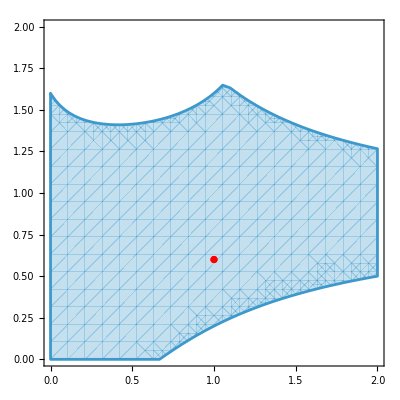

```mathematica
Show[pltr,ListPlot[{{1,3/5}},PlotStyle->Red]]
```

```mathematica
d=Reduce[cond3[[1]]<1&&Subscript[ω, n]∈Reals&&Subscript[ω, n+1]∈Reals,{Subscript[ω, n],Subscript[ω, n+1]}];
```

```mathematica
e=Reduce[cond3[[2]]<1&&Subscript[ω, n]∈Reals&&Subscript[ω, n+1]∈Reals,{Subscript[ω, n],Subscript[ω, n+1]}];
```

```mathematica
(d&&e)//Simplify;
```

#### Now let’s try finding A-stability

```mathematica
variablestepcond[3]/.{Subscript[α, n,3]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0}//Simplify
```

{1+α_(n,0)+α_(n,1)+α_(n,2)==0,(1+ω_n^2+α_(n,1)+α_(n,2)+ω_n (1+α_(n,2)))/ω_n==β_(n,3),((1+ω_n+ω_n^2)^2+α_(n,1)+(1+ω_n)^2 α_(n,2))/ω_n^2==2 (1+1/ω_n+ω_n) β_(n,3)}

```mathematica
reducedBDFLikeOrderConditions=Solve[{1+Subscript[α, n,0]+Subscript[α, n,1]+Subscript[α, n,2]==0,(1+Subscript[ω, n]^2+Subscript[α, n,1]+Subscript[α, n,2]+Subscript[ω, n] (1+Subscript[α, n,2]))/Subscript[ω, n]==Subscript[β, n,3],((1+Subscript[ω, n]+Subscript[ω, n]^2)^2+Subscript[α, n,1]+(1+Subscript[ω, n])^2 Subscript[α, n,2])/Subscript[ω, n]^2==2 (1+1/Subscript[ω, n]+Subscript[ω, n]) Subscript[β, n,3]},{Subscript[α, n,0],Subscript[α, n,1],Subscript[α, n,2]}][[1]]//Simplify
```

{α_(n,0)→-(ω_n^2 (ω_n^2+ω_n (1-2 β_(n,3))-β_(n,3)))/(1+ω_n),α_(n,1)→ω_n^3+ω_n^2 (1-2 β_(n,3))-ω_n (-1+β_(n,3))-β_(n,3),α_(n,2)→(-1-ω_n^3+2 ω_n (-1+β_(n,3))+2 ω_n^2 (-1+β_(n,3))+β_(n,3))/(1+ω_n)}

```mathematica
rhoOverSigma[x_]:=Evaluate[(∑_(j=0)^3 Subscript[α, n,j] x^j)/(∑_(j=0)^3 Subscript[β, n,j] x^j)/.reducedBDFLikeOrderConditions/.{Subscript[α, n,3]->1,Subscript[β, n,2]->0,Subscript[β, n,1]->0,Subscript[β, n,0]->0}]//Simplify
```

```mathematica
0==Numerator@rhoOverSigma[x]/.x->0//Solve
```

{{ω_n→0},{β_(n,3)→(ω_n (1+ω_n))/(1+2 ω_n)}}

#### If ω_n=1, we get the coefficient for β_2 in BDF2

```mathematica
realPartInPolar=ComplexExpand@Re[rhoOverSigma[r Exp[ⅈ θ]]/.θ->2 ArcTan[t]//ExpToTrig//TrigExpand]//Simplify
```

1/(r^3 (1+t^2)^3 (1+ω_n) β_(n,3))((-1+15 t^2-15 t^4+t^6+r (1-5 t^2-5 t^4+t^6)) ω_n^4+r (1+t^2) ω_n (1-6 t^2+t^4+r^2 (1+t^2)^2+2 r (-1+t^4)-2 (1-6 t^2+t^4+r (-1+t^4)) β_(n,3))+r (1+t^2) (r (1+t^2) (-1+r+t^2+r t^2)-(1-6 t^2+t^4+r (-1+t^4)) β_(n,3))+ω_n^3 (-1+15 t^2-15 t^4+t^6+r^2 (-1+t^2) (1+t^2)^2+2 r (1-5 t^2-5 t^4+t^6)-2 (-1+15 t^2-15 t^4+t^6+r (1-5 t^2-5 t^4+t^6)) β_(n,3))+ω_n^2 (2 r (1+t^2) (1-6 t^2+t^4+r (-1+t^4))-(-1+15 t^2-15 t^4+t^6+2 r^2 (-1+t^2) (1+t^2)^2+3 r (1-5 t^2-5 t^4+t^6)) β_(n,3)))

```mathematica
Reduce[ForAll[{t,r},r>1,realPartInPolar>0]]
```

$Aborted

```mathematica
Reduce[ForAll[{t,Subscript[ω, n]},Subscript[ω, n]>1&&r>1,realPartInPolar>=0],Reals]
```

False

#### This has also been noted in other literature, but we will simply ensure that zero stability is preserved

#### We now push into BDFL4... if Mathematica will let me

```mathematica
variablestepcond[4]/.{Subscript[α, n,4]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0,Subscript[β, n,3]->0}
```

{1+α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)==0,1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)+(α_(n,1))/ω_n+(1+1/ω_n) α_(n,2)+(1+1/ω_n+ω_(1+n)) α_(n,3)==β_(n,4),(1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n))^2+(α_(n,1))/ω_n^2+(1+1/ω_n)^2 α_(n,2)+(1+1/ω_n+ω_(1+n))^2 α_(n,3)==2 (1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)) β_(n,4)}

```mathematica
bdflcoeffs=Flatten@Solve[{1+Subscript[α, n,0]+Subscript[α, n,1]+Subscript[α, n,2]+Subscript[α, n,3]==0,1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]+Subscript[α, n,1]/Subscript[ω, n]+(1+1/Subscript[ω, n]) Subscript[α, n,2]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n]) Subscript[α, n,3]==Subscript[β, n,4],(1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n])^2+Subscript[α, n,1]/Subscript[ω, n]^2+(1+1/Subscript[ω, n])^2 Subscript[α, n,2]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n])^2 Subscript[α, n,3]==2 (1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]) Subscript[β, n,4]},{Subscript[α, n,0],Subscript[α, n,1],Subscript[α, n,2]}]//Simplify
```

{α_(n,0)→-(ω_n^2 (ω_(1+n)^2 (1+2 ω_(2+n)+ω_(2+n)^2+α_(n,3))+ω_(1+n) (1+α_(n,3)+ω_(2+n) (1-2 β_(n,4))-2 β_(n,4))-β_(n,4)))/(1+ω_n),α_(n,1)→ω_n ω_(1+n)^2 (1+2 ω_(2+n)+ω_(2+n)^2+α_(n,3))+ω_(1+n) (1+ω_(2+n)+α_(n,3)+ω_n (1+α_(n,3)+ω_(2+n) (1-2 β_(n,4))-2 β_(n,4)))-(1+ω_n) β_(n,4),α_(n,2)→-(1+α_(n,3)+ω_(1+n) (1+ω_(2+n)+α_(n,3))-β_(n,4)+ω_n (1+α_(n,3)+ω_(1+n)^2 (1+2 ω_(2+n)+ω_(2+n)^2+α_(n,3))-2 β_(n,4)-2 ω_(1+n) (-1-α_(n,3)+ω_(2+n) (-1+β_(n,4))+β_(n,4))))/(1+ω_n)}

```mathematica
{Subscript[α, n,0]->-1/(1+Subscript[ω, n])Subscript[ω, n]^2 (Subscript[ω, 1+n]^2 (1+2 Subscript[ω, 2+n]+Subscript[ω, 2+n]^2+Subscript[α, n,3])+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[ω, 2+n] (1-2 Subscript[β, n,4])-2 Subscript[β, n,4])-Subscript[β, n,4]),Subscript[α, n,1]->Subscript[ω, n] Subscript[ω, 1+n]^2 (1+2 Subscript[ω, 2+n]+Subscript[ω, 2+n]^2+Subscript[α, n,3])+Subscript[ω, 1+n] (1+Subscript[ω, 2+n]+Subscript[α, n,3]+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[ω, 2+n] (1-2 Subscript[β, n,4])-2 Subscript[β, n,4]))-(1+Subscript[ω, n]) Subscript[β, n,4],Subscript[α, n,2]->-1/(1+Subscript[ω, n])(1+Subscript[α, n,3]+Subscript[ω, 1+n] (1+Subscript[ω, 2+n]+Subscript[α, n,3])-Subscript[β, n,4]+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[ω, 1+n]^2 (1+2 Subscript[ω, 2+n]+Subscript[ω, 2+n]^2+Subscript[α, n,3])-2 Subscript[β, n,4]-2 Subscript[ω, 1+n] (-1-Subscript[α, n,3]+Subscript[ω, 2+n] (-1+Subscript[β, n,4])+Subscript[β, n,4])))}//FullSimplify
```

{α_(n,0)→(ω_n^2 (β_(n,4)-ω_(1+n) (1+ω_(2+n)+α_(n,3)+ω_(1+n) ((1+ω_(2+n))^2+α_(n,3))-2 (1+ω_(2+n)) β_(n,4))))/(1+ω_n),α_(n,1)→ω_n ω_(1+n)^2 ((1+ω_(2+n))^2+α_(n,3))-(1+ω_n) β_(n,4)+ω_(1+n) ((1+ω_n) (1+ω_(2+n)+α_(n,3))-2 ω_n (1+ω_(2+n)) β_(n,4)),α_(n,2)→(-1-α_(n,3)-ω_(1+n) (1+ω_(2+n)+α_(n,3))+β_(n,4)+ω_n (-(1+ω_(1+n) (1+ω_(2+n)))^2-(1+ω_(1+n))^2 α_(n,3)+2 (1+ω_(1+n) (1+ω_(2+n))) β_(n,4)))/(1+ω_n)}

```mathematica
-2/41(18+11 √2)//TeXForm
```

\frac{4}{41} \left(10-3 \sqrt{2}\right)

```mathematica
rho=ρ[{Subscript[α, n,0],Subscript[α, n,1],Subscript[α, n,2],Subscript[α, n,3],1}][ζ]/.bdflcoeffs;
```

ReplaceAll::reps: {bdflcoeffs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Clear[cond4,g]
```

```mathematica
cond4=Abs[ζ/.Solve[rho==0,ζ]//Simplify]//Simplify;
```

```mathematica
con4p1=(cond4[[2]]/.{Subscript[β, n,4]->4/41(10-3 √2),Subscript[α, n,3]->-2/41(18+11 √2)})/.{Subscript[ω, n+2]->wn2,Subscript[ω, n+1]->wn1,Subscript[ω, n]->wn}//Simplify;
```

Part::partw: Part 2 of Abs[ζ] does not exist.

```mathematica
con4p2=(cond4[[3]]/.{Subscript[β, n,4]->4/41(10-3 √2),Subscript[α, n,3]->-2/41(18+11 √2)})/.{Subscript[ω, n+2]->wn2,Subscript[ω, n+1]->wn1,Subscript[ω, n]->wn}//Simplify;
```

```mathematica
con4p3=(cond4[[4]]/.{Subscript[β, n,4]->4/41(10-3 √2),Subscript[α, n,3]->-2/41(18+11 √2)})/.{Subscript[ω, n+2]->wn2,Subscript[ω, n+1]->wn1,Subscript[ω, n]->wn}//Simplify;
```

```mathematica
RegionPlot3D[con4p1<1&&con4p2<1&&con4p3<1,{wn2,0,2},{wn1,0,2},{wn,0,2},AxesLabel->{Subscript[ω, n+2],Subscript[ω, n+1],Subscript[ω, n]}]
```

-Graphics3D-

```mathematica
variablestepcond[5]/.{Subscript[α, n,5]->1,Subscript[β, n,0]->0,Subscript[β, n,1]->0,Subscript[β, n,2]->0,Subscript[β, n,3]->0,Subscript[β, n,4]->0}
```

{1+α_(n,0)+α_(n,1)+α_(n,2)+α_(n,3)+α_(n,4)==0,1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)+ω_(1+n) ω_(2+n) ω_(3+n)+(α_(n,1))/ω_n+(1+1/ω_n) α_(n,2)+(1+1/ω_n+ω_(1+n)) α_(n,3)+(1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)) α_(n,4)==β_(n,5),(1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)+ω_(1+n) ω_(2+n) ω_(3+n))^2+(α_(n,1))/ω_n^2+(1+1/ω_n)^2 α_(n,2)+(1+1/ω_n+ω_(1+n))^2 α_(n,3)+(1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n))^2 α_(n,4)==2 (1+1/ω_n+ω_(1+n)+ω_(1+n) ω_(2+n)+ω_(1+n) ω_(2+n) ω_(3+n)) β_(n,5)}

```mathematica
coeffs5step=Flatten@Solve[{1+Subscript[α, n,0]+Subscript[α, n,1]+Subscript[α, n,2]+Subscript[α, n,3]+Subscript[α, n,4]==0,1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]+Subscript[ω, 1+n] Subscript[ω, 2+n] Subscript[ω, 3+n]+Subscript[α, n,1]/Subscript[ω, n]+(1+1/Subscript[ω, n]) Subscript[α, n,2]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n]) Subscript[α, n,3]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]) Subscript[α, n,4]==Subscript[β, n,5],(1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]+Subscript[ω, 1+n] Subscript[ω, 2+n] Subscript[ω, 3+n])^2+Subscript[α, n,1]/Subscript[ω, n]^2+(1+1/Subscript[ω, n])^2 Subscript[α, n,2]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n])^2 Subscript[α, n,3]+(1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n])^2 Subscript[α, n,4]==2 (1+1/Subscript[ω, n]+Subscript[ω, 1+n]+Subscript[ω, 1+n] Subscript[ω, 2+n]+Subscript[ω, 1+n] Subscript[ω, 2+n] Subscript[ω, 3+n]) Subscript[β, n,5]},{Subscript[α, n,0],Subscript[α, n,1],Subscript[α, n,2]}]//Simplify
```

{α_(n,0)→-(ω_n^2 (ω_(1+n)^2 (1+α_(n,3)+α_(n,4)+2 ω_(2+n) (1+ω_(3+n)+α_(n,4))+ω_(2+n)^2 (1+2 ω_(3+n)+ω_(3+n)^2+α_(n,4)))+ω_(1+n) (1+α_(n,3)+α_(n,4)+ω_(2+n) (1+α_(n,4)+ω_(3+n) (1-2 β_(n,5))-2 β_(n,5))-2 β_(n,5))-β_(n,5)))/(1+ω_n),α_(n,1)→ω_n ω_(1+n)^2 (1+α_(n,3)+α_(n,4)+2 ω_(2+n) (1+ω_(3+n)+α_(n,4))+ω_(2+n)^2 (1+2 ω_(3+n)+ω_(3+n)^2+α_(n,4)))+ω_(1+n) (1+α_(n,3)+α_(n,4)+ω_(2+n) (1+ω_(3+n)+α_(n,4))+ω_n (1+α_(n,3)+α_(n,4)+ω_(2+n) (1+α_(n,4)+ω_(3+n) (1-2 β_(n,5))-2 β_(n,5))-2 β_(n,5)))-(1+ω_n) β_(n,5),α_(n,2)→-1/(1+ω_n)(1+α_(n,3)+α_(n,4)+ω_(1+n) (1+α_(n,3)+α_(n,4)+ω_(2+n) (1+ω_(3+n)+α_(n,4)))+ω_n (1+α_(n,3)+α_(n,4)+ω_(1+n)^2 (1+α_(n,3)+α_(n,4)+2 ω_(2+n) (1+ω_(3+n)+α_(n,4))+ω_(2+n)^2 (1+2 ω_(3+n)+ω_(3+n)^2+α_(n,4)))+2 ω_(1+n) (1+α_(n,3)+α_(n,4)+ω_(2+n) (1+α_(n,4)-ω_(3+n) (-1+β_(n,5))-β_(n,5))-β_(n,5))-2 β_(n,5))-β_(n,5))}

```mathematica
{Subscript[α, n,0]->-1/(1+Subscript[ω, n])Subscript[ω, n]^2 (Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]+Subscript[ω, 3+n] (1-2 Subscript[β, n,5])-2 Subscript[β, n,5])-2 Subscript[β, n,5])-Subscript[β, n,5]),Subscript[α, n,1]->Subscript[ω, n] Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]+Subscript[ω, 3+n] (1-2 Subscript[β, n,5])-2 Subscript[β, n,5])-2 Subscript[β, n,5]))-(1+Subscript[ω, n]) Subscript[β, n,5],Subscript[α, n,2]->-1/(1+Subscript[ω, n])(1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4]))+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+2 Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]-Subscript[ω, 3+n] (-1+Subscript[β, n,5])-Subscript[β, n,5])-Subscript[β, n,5])-2 Subscript[β, n,5])-Subscript[β, n,5])}/.{Subscript[ω, n+3]->omega3,Subscript[ω, n+2]->omega2,Subscript[ω, n+1]->omega1,Subscript[ω, n]->omega,Subscript[β, n,5]->beta,Subscript[α, n,4]->alpha,Subscript[α, n,3]->alpha5}
```

{α_(n,0)→-1/(1+omega)omega^2 (-beta+omega1 (1+alpha+alpha5-2 beta+omega2 (1+alpha-2 beta+(1-2 beta) omega3))+omega1^2 (1+alpha+alpha5+2 omega2 (1+alpha+omega3)+omega2^2 (1+alpha+2 omega3+omega3^2))),α_(n,1)→-beta (1+omega)+omega omega1^2 (1+alpha+alpha5+2 omega2 (1+alpha+omega3)+omega2^2 (1+alpha+2 omega3+omega3^2))+omega1 (1+alpha+alpha5+omega2 (1+alpha+omega3)+omega (1+alpha+alpha5-2 beta+omega2 (1+alpha-2 beta+(1-2 beta) omega3))),α_(n,2)→-1/(1+omega)(1+alpha+alpha5-beta+omega1 (1+alpha+alpha5+omega2 (1+alpha+omega3))+omega (1+alpha+alpha5-2 beta+2 omega1 (1+alpha+alpha5-beta+omega2 (1+alpha-beta-(-1+beta) omega3))+omega1^2 (1+alpha+alpha5+2 omega2 (1+alpha+omega3)+omega2^2 (1+alpha+2 omega3+omega3^2))))}

```mathematica
{Subscript[α, n,0]->-1/(1+Subscript[ω, n])Subscript[ω, n]^2 (Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]+Subscript[ω, 3+n] (1-2 Subscript[β, n,5])-2 Subscript[β, n,5])-2 Subscript[β, n,5])-Subscript[β, n,5]),Subscript[α, n,1]->Subscript[ω, n] Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]+Subscript[ω, 3+n] (1-2 Subscript[β, n,5])-2 Subscript[β, n,5])-2 Subscript[β, n,5]))-(1+Subscript[ω, n]) Subscript[β, n,5],Subscript[α, n,2]->-1/(1+Subscript[ω, n])(1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4]))+Subscript[ω, n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 1+n]^2 (1+Subscript[α, n,3]+Subscript[α, n,4]+2 Subscript[ω, 2+n] (1+Subscript[ω, 3+n]+Subscript[α, n,4])+Subscript[ω, 2+n]^2 (1+2 Subscript[ω, 3+n]+Subscript[ω, 3+n]^2+Subscript[α, n,4]))+2 Subscript[ω, 1+n] (1+Subscript[α, n,3]+Subscript[α, n,4]+Subscript[ω, 2+n] (1+Subscript[α, n,4]-Subscript[ω, 3+n] (-1+Subscript[β, n,5])-Subscript[β, n,5])-Subscript[β, n,5])-2 Subscript[β, n,5])-Subscript[β, n,5])}/.{Subscript[ω, n+3]->1,Subscript[ω, n+2]->1,Subscript[ω, n+1]->1,Subscript[ω, n]->1,Subscript[β, n,5]->5/44(7-√5),Subscript[α, n,4]->-1/44(45+14 √5),Subscript[α, n,3]->(√5)/2}//Simplify
```

{α_(n,0)→1/88 (-13+5 √5),α_(n,1)→1/22 (10-3 √5),α_(n,2)→1/88 (-25-9 √5)}

```mathematica
5/44(7-√5)//TeXForm
```

\frac{5}{44} \left(7-\sqrt{5}\right)

```mathematica
rho5=ρ[{Subscript[α, n,0],Subscript[α, n,1],Subscript[α, n,2],Subscript[α, n,3],Subscript[α, n,4],1}][ζ]/.coeffs5step;
```

#### Just for this case, let’s assume a constant step size ratio for Robertson’s problem

```mathematica
cond5=Abs[ζ/.Solve[rho5==0,ζ]]/.{Subscript[β, n,5]->5/44(7-√5),Subscript[α, n,4]->-1/44(45+14 √5),Subscript[α, n,3]->(√5)/2}/.{Subscript[ω, n+3]->wn,Subscript[ω, n+2]->wn,Subscript[ω, n+1]->wn1,Subscript[ω, n]->wn}
```

```mathematica
con5p1=cond5[[2]];
```

```mathematica
con5p2=cond5[[3]];
```

```mathematica
con5p3=cond5[[4]];
```

```mathematica
con5p4=cond5[[5]];
```

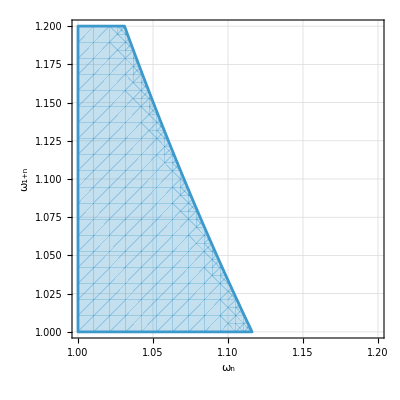

```mathematica
RegionPlot[con5p1<1&&con5p2<1&&con5p3<1&&con5p4<1,{wn,1,6/5},{wn1,1,6/5},FrameLabel->{Subscript[ω, n],Subscript[ω, n+1]},RotateLabel->False,GridLines->Automatic]
```

```mathematica
NSolve[10^(14/n)==1.05,n]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{n→0.000813054-0.732935 ⅈ},{n→0.00110666-0.85509 ⅈ},{n→0.00110666+0.85509 ⅈ},{n→0.00159358-1.02611 ⅈ},{n→0.00159358+1.02611 ⅈ},{n→0.00248997-1.28263 ⅈ},{n→0.00248997+1.28263 ⅈ},{n→0.00442661-1.71017 ⅈ},{n→0.00442661+1.71017 ⅈ},{n→0.00995978-2.56524 ⅈ},{n→0.00995978+2.56524 ⅈ},{n→0.0398373-5.13024 ⅈ},{n→0.0398373+5.13024 ⅈ},{n→660.711}}

```mathematica
N[(1+1/2 k λ)/(1-1/2 k λ)]/.{k->0.1,λ->-10^6}
```

-0.99996

```mathematica
N[(1-k λ)^-1]/.{k->0.1,λ->-10^6}
```

9.9999×10^-6